```mathematica
(* Mathematica*)
<<ComputationalGeometry`
```

```mathematica
(*Orbifold tetrahedron page 406 Reid and Maclachlan*)
```

```mathematica
pa[x_]=x^4-3*x^3+7*x^2-5*x+1
pts=Union[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pa[x]==0,x]]
```

1-5 x+7 x^2-3 x^3+x^4

{{0.351405,-0.665609,-0.658392},{0.351405,0.665609,-0.658392},{0.615502,0.,0.788135},{0.881262,0.,0.472628}}

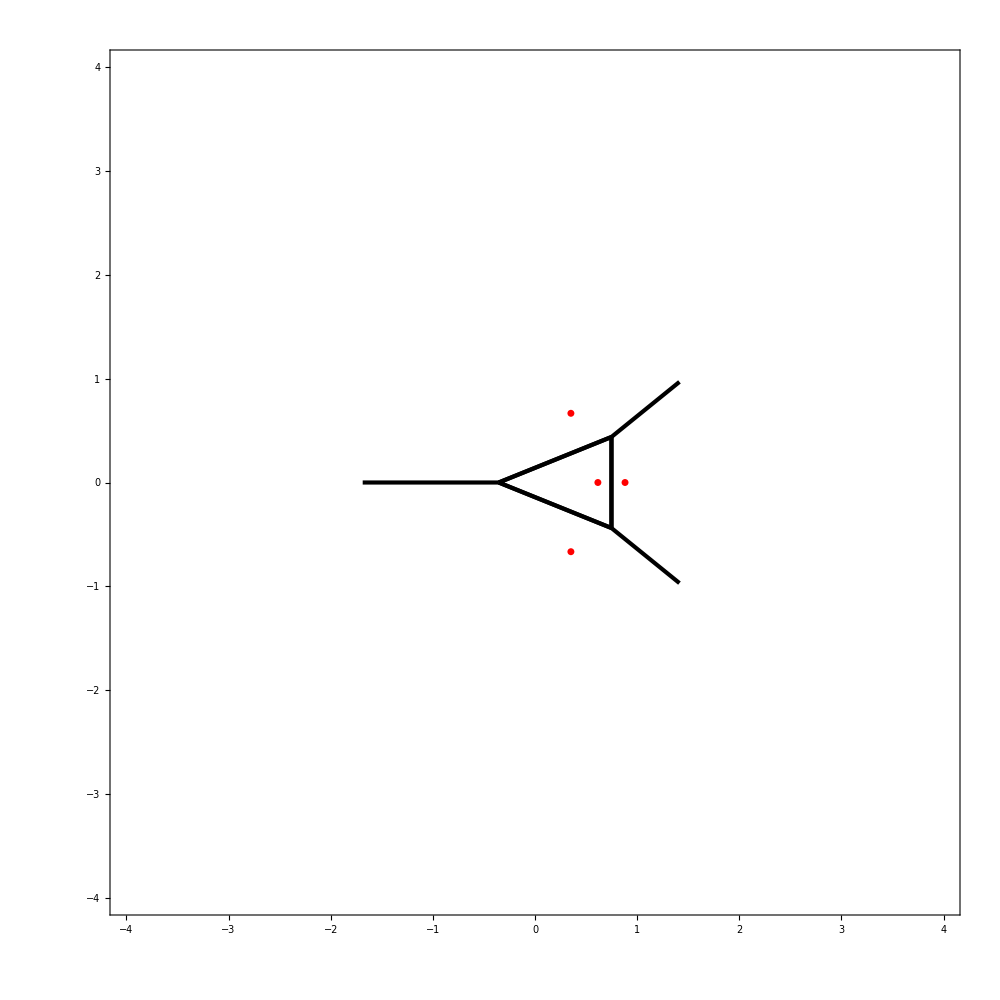

-Graphics3D-

4

-Graphics3D-

```mathematica
ptsn=Table[Hue[Norm[x/.NSolve[pa[x]==0,x][[i]]]],{i,Length[pts]}];
(* Voronoi diagram*)
g1=Show[{
DiagramPlot[Most/@pts,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[Most/@pts]}]
},PlotRange->{{-4,4},{-4,4}},Frame->True,PlotRangeClipping->True,ImageSize->1000]
(* 3d projection of polyhedron*)
Show[Graphics3D[{Red,PointSize[0.0375],Point/@pts}],Axes->True]
(* convex hull: MathWorld Library*)
<<ConvexHull`
hull0=ConvexHull3D[pts];
Length[hull0]
hull1=Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{Hue[1],hull0[[i]]}],{i,Length[hull0]}]];
Graphics3D[hull={Opacity[0.5],hull1},ImageSize->1000,Boxed->False,Background->Black,ViewPoint->Top]
(* end*)
```